```mathematica
Exit
```

```mathematica
If[
FileExistsQ[#],DeleteDirectory[#,DeleteContents->True]
]&[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"LibraryResources",$SystemID}]]

Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]

SphereVolume[d_]:=2 Power[Pi,(d+1)/2]/Gamma[(d+1)/2];
BallVolume[d_]:=Power[Pi,d/2]/Gamma[d/2+1];
SOVolume[d_]:=Product[SphereVolume[n],{n,1,d-1}];
```

```mathematica
Quiet[LibraryFunctionUnload[cSOVolume]];
ClearAll[cSOVolume];
cSOVolume = Module[{lib, libname, name, code, t},

	libname = name = "cSOVolume";

	lib = FileNameJoin[{CycleSamplerLink`Private`$libraryDirectory, libname<>CCompilerDriver`CCompilerDriverBase`$PlatformDLLExtension}];
	
	If[True,

		Print["Compiling "<>name<>"..."];

		code = StringJoin[
"
// This is the actual C++ code.

#define NDEBUG

//#define TOOLS_ENABLE_PROFILER

#include \"WolframLibrary.h\"
#include \"MMA.h\"

#include \"CycleSampler.hpp\"

using namespace Tools;
using namespace Tensors;
using namespace CycleSampler;
using namespace mma;

using Real = mreal;
using Int  = mint;

EXTERN_C DLLEXPORT int "<>name<>"(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res )
{
	//Profiler::Clear(\""<>$HomeDirectory<>"\");

	get<Real>(Res) = SOVolume<Real>(get<Int>(Args[0]));

	return LIBRARY_NO_ERROR;
}"];
		
		(* Invoke CreateLibrary to compile the C++ code. *)
		t = AbsoluteTiming[
			lib = CreateLibrary[
				code,
				libname,
				"Language"->"C++",
				"TargetDirectory"-> CycleSamplerLink`Private`$libraryDirectory,
				(*"ShellCommandFunction"->Print,*)
				(*"ShellOutputFunction"->Print,*)
				CycleSamplerLink`Private`$compilationOptions
			]
		][[1]];
		Print["Compilation done. Time elapsed = ", t, " s.\n"];
	];
	
	(* Load the resulting dynamic libary into the Mathematica session; use memoization to quickly look up already loaded libraries.*)
	LibraryFunctionLoad[lib,name,
		{Integer},
		Real
	]
];
```

Compiling cSOVolume...

Reading build settings from /Users/Henrik/github/CycleSamplerLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 0.807495 s.

```mathematica
c=Table[N[SOVolume[d],100]/Power[2,d(d-1)/4],{d,1,2 2 64}];//AbsoluteTiming
```

{0.214324,Null}

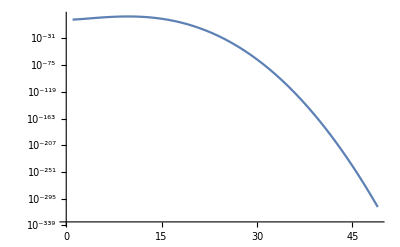

```mathematica
ListLinePlot[{c},PlotRange->All,ScalingFunctions->"Log"]
```

{0.208131,Null}

{0.003242,Null}

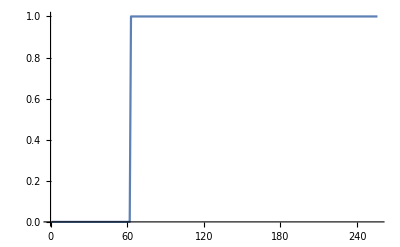

```mathematica
a=Table[N[SOVolume[d],100],{d,1,2 2 64}];//AbsoluteTiming
b=Table[SetPrecision[cSOVolume[d],100],{d,1,2 2 64}];//AbsoluteTiming

ListLinePlot[Abs[a-b]/a]
```

```mathematica
Log[a]
```

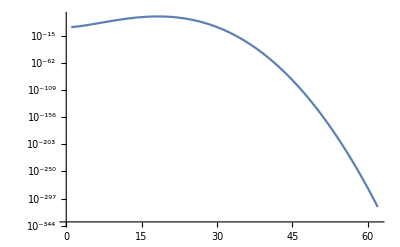

```mathematica
ListLinePlot[a,PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
a//Dimensions
```

{256}

```mathematica
Quiet[LibraryFunctionUnload[cGammaQuotient]];
ClearAll[cGammaQuotient];
cGammaQuotient = Module[{lib, libname, name, code, t},

	libname = name = "cGammaQuotient";

	lib = FileNameJoin[{CycleSamplerLink`Private`$libraryDirectory, libname<>CCompilerDriver`CCompilerDriverBase`$PlatformDLLExtension}];
	
	If[True,

		Print["Compiling "<>name<>"..."];

		code = StringJoin[
"
// This is the actual C++ code.

#define NDEBUG

//#define TOOLS_ENABLE_PROFILER

#include \"WolframLibrary.h\"
#include \"MMA.h\"

#include \"CycleSampler.hpp\"

using namespace Tools;
using namespace Tensors;
using namespace CycleSampler;

using Real = mreal;
using Int  = mint;

EXTERN_C DLLEXPORT int "<>name<>"(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res )
{
	//Profiler::Clear(\""<>$HomeDirectory<>"\");

	Real x = mma::get<Real>(Args[0]);
	Real a = mma::get<Real>(Args[1]);
	Real result = GammaQuotient<Real>( x, a );

	mma::get<Real>(Res) = result;
	
	return LIBRARY_NO_ERROR;
}"];
		
		(* Invoke CreateLibrary to compile the C++ code. *)
		t = AbsoluteTiming[
			lib = CreateLibrary[
				code,
				libname,
				"Language"->"C++",
				"TargetDirectory"-> CycleSamplerLink`Private`$libraryDirectory,
				(*"ShellCommandFunction"->Print,*)
				(*"ShellOutputFunction"->Print,*)
				CycleSamplerLink`Private`$compilationOptions
			]
		][[1]];
		Print["Compilation done. Time elapsed = ", t, " s.\n"];
	];
	
	(* Load the resulting dynamic libary into the Mathematica session; use memoization to quickly look up already loaded libraries.*)
	LibraryFunctionLoad[lib,name,
		{Real,Real},
		Real
	]
];
```

Compiling cGammaQuotient...

Compilation done. Time elapsed = 0.81616 s.

0.989621

```mathematica
a=Table[N[Gamma[d+1/2]/Gamma[d],16],{d,1,100000,1000}];//AbsoluteTiming
```

{0.674803,Null}

```mathematica
b=Table[cGammaQuotient[d,0.5],{d,1.,100000,1000}];//AbsoluteTiming
```

{0.032407,Null}

```mathematica
Max[Abs[a-b]/a]
```

2.94405×10^-14

```mathematica
data=RandomClosedPolygons[d,r,1000,"SphereRadii"->"SymplecticQuotient"];
```

Compiling cRandomClosedPolygons[3]...

Compilation done. Time elapsed = 2.17372 s.

```mathematica
SphereVolume[d-1]
```

```mathematica
"3.279162005060144"
```

```mathematica
Gamma[0]
```

ComplexInfinity

```mathematica
cSphereVolume[]
```

```mathematica
SphereVolume/@Range[0.,11.]
BallVolume/@Range[0.,11.]
N[SOVolume/@Range[0.,11.]]
```

```mathematica
{1.,1.,6.283185307179586,78.95683520871486,1558.5454565440389,41019.27225921297,1.2718549048937047*^6,4.2064517416885994*^7,1.365822135454276*^9,4.054658826018169*^10,1.0340045132082826*^12,2.1429891061066293*^13}
```

```mathematica
SOVolume[d_]:=Product[SphereVolume[n-1],{n,2,d}]
```

```mathematica
SOVolume[10]
```

```mathematica
4./3 Pi
```

```mathematica
11!
```

```mathematica
0!
```

```mathematica
2 Power[Pi,2n+1]/(2n)!/(2 Power[2Pi,2n]/(2n-1)!!)//Simplify
```

```mathematica
sphereVolume[0]=2;
sphereVolume[n]=sphereVolume[n-1]Pi/;
```

```mathematica
?Factorial2
```

```mathematica
d=.
```

```mathematica
Solve[d==2n+1,n]
```

```mathematica
SphereVolume[d_?OddQ]:=With[{n=(d-1)/2},2 Power[Pi,n+1]/n!];
SphereVolume[d_?EvenQ]:=With[{n=d/2},2 Power[2Pi,n]/(d-1)!!];
```

```mathematica
aa=Table[d->N@TrueSphereVolume[d],{d,1,10}]
Table[n->N@SphereVolume[n],{n,1,10}]
```

```mathematica
Ratios[Values[aa]]
```

```mathematica
ClearAll[λ];
χ[r_]:=λ 2^d(1-r^2)^(n(d-1)-d)
λ=λ/.Solve[FullSimplify[
SphereVolume[d-1]Integrate[χ[r] r^(d-1),{r,0,1},Assumptions->d>1&&n>1&&d∈Integers&&n∈Integers],
d>0&&n>0&&d∈Integers&&n∈Integers
]==1,λ][[1]]
```

(2^-d π^(-d/2) Gamma[1+d (-1/2+n)-n])/Gamma[(-1+d) (-1+n)]

```mathematica
1+d (-1/2+n)-n//Expand
```

1-d/2-n+d n

```mathematica
(-1+d) (-1+n)+d/2//Expand
```

1-d/2-n+d n

```mathematica
SphereVolume[d]
```

```mathematica
λ/.{d->4,n->120}
```

```mathematica
1+d (-1/2+n)-n//Expand
```

```mathematica
(-1+d) (-1+n)//Expand//Simplify
```

```mathematica
χ[r] r^(d-1)//Expand
```

```mathematica
1+d (-1/2+n)-n//Expand
```

```mathematica
(-1+d) (-1+n)//Expand
```

```mathematica
Table[Gamma[x+1/2]/Gamma[x],{x,1,10}]
```

```mathematica
Plot[{Gamma[x+1/2]/Gamma[x] Sqrt[x]},{x,1,10}]
```

```mathematica
BallVolume[d]
```

```mathematica
Integrate[χ[r] r^(d-1),{r,0,1},Assumptions->d>0&&n>0&&d∈Integers&&n∈Integers]
```

```mathematica
Gamma[2]
Gamma[3]
```

1

2

```mathematica
Ratios@Table[Gamma[k+1/2],{k,0,10}]
Table[k+1/2,{k,0,10}]
```

{1/2,3/2,5/2,7/2,9/2,11/2,13/2,15/2,17/2,19/2}

{1/2,3/2,5/2,7/2,9/2,11/2,13/2,15/2,17/2,19/2,21/2}

```mathematica
Gamma[1/2]
Gamma[1+1/2]
Gamma[2+1/2]
Gamma[3+1/2]
```

√π

(√π)/2

(3 √π)/4

(15 √π)/8